# Phase Space of f(R) Gravity In The Presence Of Thermal Effects

## 1. Introduction

This code was devised in order to study the behavior of an f(R) gravity assumming that a thermal term is present in Friedmann’s equation. References to such equation can be found in arXiv:2009.12897. There exists 6 variables in total however for simplicity we shall limit our work to only 4. So, as a first step, one must construct the system of nonlinear differential equations. The aforementioned problem is described by the following equations.

### 1.1 Differential equations.

```mathematica
f1[x1_,x2_,x3_,x4_]:=x1(x1-x3+3)+2(x3-2)(1-2 x4);
f2[x1_,x2_,x3_,x4_]:=x2(x1-2 x3+4)-4(x3-2)+m;
f3[x1_,x2_,x3_,x4_]:=-m-2(x3-2)^2;
f4[x1_,x2_,x3_,x4_]:=x4(x1+2 x3-4);
```

The above system has uknown for the time being fixed points, however some of them may be intrinsically unrealistic. In order to ascertain whether such possibility exists, one needs to examine whether such fixed points satisfy the Friedmann equation. In consequence, the constraint below suggests that when it is equal to unity, the fixed point is physical.

### 1.2 Validity Of Fixed Points.

```mathematica
Constraint = x1+x2+x3+x4;
```

## 2. Qualitative Aspects

As a first step, the fixed points are identified. Naturally, a fixed point is derived as a root of the previous equations. For simplicity, we study the matter dominated era of the universe, which corresponds to a value of m equal to -4.5. Other cosmological eras can be studied as well, for instance a quasi de-Sitter expansion, or the inflationary era, correspond to the value m=0 whereas the radiation dominated era to m=-8. One needs however to examine whether such fixed points are physical, as mentioned before.

### 2.1 The fixed points

```mathematica
s=Solve[{f1[x1,x2,x3,x4]==0,f2[x1,x2,x3,x4]==0,f3[x1,x2,x3,x4]==0,f4[x1,x2,x3,x4]==0},{x1,x2,x3,x4}]//Simplify;
m=-9/2;
equ1=s[[1]];
equ2=s[[2]];
equ3=s[[3]];
equ4=s[[6]];
c1=Constraint/.equ1//N
c2=Constraint/.equ2//N
c3=Constraint/.equ3//N
c4=Constraint/.equ4//N
```

1.

1.

1.

«1 more identical outputs»

### 2.2 Stability Of Fixed Points.

In order to ascertain whether a fixed point is stable or not, the Hartman-Grobman theorem is implimented. Accordingly, one examines the linearised system near a fixed point and provided that the eigenvalues of the Jacobian matrix have nonzero real part, then the stability of the linearised system is topologically equivalent to that of the nonlinear system. The difference between the two pictures resides in the actual trajectories of the solution.

```mathematica
J=({{D[f1[x1,x2,x3,x4],x1], D[f1[x1,x2,x3,x4],x2], D[f1[x1,x2,x3,x4],x3], D[f1[x1,x2,x3,x4],x4]}, {D[f2[x1,x2,x3,x4],x1], D[f2[x1,x2,x3,x4],x2], D[f2[x1,x2,x3,x4],x3], D[f2[x1,x2,x3,x4],x4]}, {D[f3[x1,x2,x3,x4],x1], D[f3[x1,x2,x3,x4],x2], D[f3[x1,x2,x3,x4],x3], D[f3[x1,x2,x3,x4],x4]}, {D[f4[x1,x2,x3,x4],x1], D[f4[x1,x2,x3,x4],x2], D[f4[x1,x2,x3,x4],x3], D[f4[x1,x2,x3,x4],x4]}});
```

```mathematica
equ1//Simplify;
A1=J/.equ1;
MatrixForm[A1]//N;
Eigenvalues[A1]//N;
Eigenvectors[A1]//N;
```

```mathematica
equ2//Simplify;
A2=J/.equ2;
MatrixForm[A2]//N;
Eigenvalues[A2]//N;
Eigenvectors[A2]//N;
```

```mathematica
equ3//Simplify;
A3=J/.equ3;
MatrixForm[A3]//N;
Eigenvalues[A3]//N;
Eigenvectors[A3]//N;
```

```mathematica
equ4//Simplify;
A4=J/.equ4;
MatrixForm[A4]//N;
Eigenvalues[A4]//N;
Eigenvectors[A4]//N;
```

## 3. Numerical Results.

We now proceed with the phase space analysis. Random trajectories are chosen for the 4 variables. For this procedure, the system of differential equations is olved numerically for the choice of such initial conditions. Here, t is an auxiliary variable,  not to be confused with time, that described the e-folds.  Firstly, the sets to be integrated are introduced for simplicity, afterwards they are solved and finally certain plots are presented seperately and in 3D and 2D phase space.

NDSolve::ndsz: At t == 0.811705, step size is effectively zero; singularity or stiff system suspected.

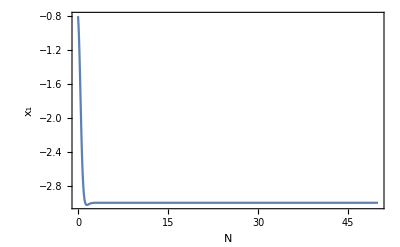

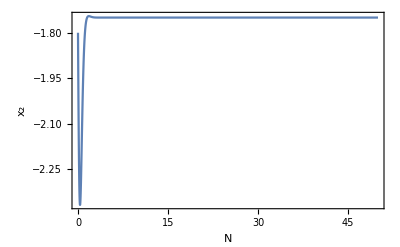

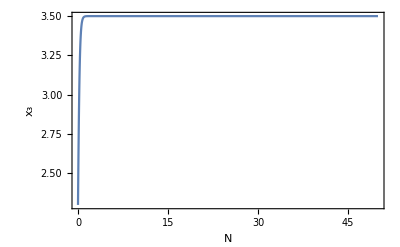

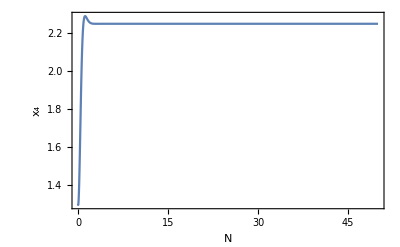

{-3.}

{-1.75}

{3.5}

{2.25}

{1.}

```mathematica
ivp01={x1'[t]==f1[x1[t],x2[t],x3[t],x4[t]],x2'[t]==f2[x1[t],x2[t],x3[t],x4[t]],x3'[t]==f3[x1[t],x2[t],x3[t],x4[t]],x4'[t]==f4[x1[t],x2[t],x3[t],x4[t]],x1[0]==-1.5,x2[0]==-1.5,x3[0]==2.7,x4[0]==0.7};
ivp02={x1'[t]==f1[x1[t],x2[t],x3[t],x4[t]],x2'[t]==f2[x1[t],x2[t],x3[t],x4[t]],x3'[t]==f3[x1[t],x2[t],x3[t],x4[t]],x4'[t]==f4[x1[t],x2[t],x3[t],x4[t]],x1[0]==-1.1,x2[0]==-1.4,x3[0]==2.7,x4[0]== 0.8};
ivp03={x1'[t]==f1[x1[t],x2[t],x3[t],x4[t]],x2'[t]==f2[x1[t],x2[t],x3[t],x4[t]],x3'[t]==f3[x1[t],x2[t],x3[t],x4[t]],x4'[t]==f4[x1[t],x2[t],x3[t],x4[t]],x1[0]==0.4,x2[0]==-1.1,x3[0]==2.4,x4[0]== 0.1};
ivp04={x1'[t]==f1[x1[t],x2[t],x3[t],x4[t]],x2'[t]==f2[x1[t],x2[t],x3[t],x4[t]],x3'[t]==f3[x1[t],x2[t],x3[t],x4[t]],x4'[t]==f4[x1[t],x2[t],x3[t],x4[t]],x1[0]==-1.4,x2[0]==-0.8,x3[0]==2.4,x4[0]==0.8};
ivp05={x1'[t]==f1[x1[t],x2[t],x3[t],x4[t]],x2'[t]==f2[x1[t],x2[t],x3[t],x4[t]],x3'[t]==f3[x1[t],x2[t],x3[t],x4[t]],x4'[t]==f4[x1[t],x2[t],x3[t],x4[t]],x1[0]==-1.1,x2[0]==-0.7,x3[0]==1.7,x4[0]==1.1};
ivp06={x1'[t]==f1[x1[t],x2[t],x3[t],x4[t]],x2'[t]==f2[x1[t],x2[t],x3[t],x4[t]],x3'[t]==f3[x1[t],x2[t],x3[t],x4[t]],x4'[t]==f4[x1[t],x2[t],x3[t],x4[t]],x1[0]==-1.2,x2[0]==-1,x3[0]==2.1,x4[0]==0.1};
ivp07={x1'[t]==f1[x1[t],x2[t],x3[t],x4[t]],x2'[t]==f2[x1[t],x2[t],x3[t],x4[t]],x3'[t]==f3[x1[t],x2[t],x3[t],x4[t]],x4'[t]==f4[x1[t],x2[t],x3[t],x4[t]],x1[0]==-0.8,x2[0]==-1.1,x3[0]==2.1,x4[0]==0.8};
ivp08={x1'[t]==f1[x1[t],x2[t],x3[t],x4[t]],x2'[t]==f2[x1[t],x2[t],x3[t],x4[t]],x3'[t]==f3[x1[t],x2[t],x3[t],x4[t]],x4'[t]==f4[x1[t],x2[t],x3[t],x4[t]],x1[0]==-1.7,x2[0]==-1,x3[0]==2.4,x4[0]==1.3};
ivp09={x1'[t]==f1[x1[t],x2[t],x3[t],x4[t]],x2'[t]==f2[x1[t],x2[t],x3[t],x4[t]],x3'[t]==f3[x1[t],x2[t],x3[t],x4[t]],x4'[t]==f4[x1[t],x2[t],x3[t],x4[t]],x1[0]==-1.2,x2[0]==-0.8,x3[0]==0.5,x4[0]==2.5};
ivp10={x1'[t]==f1[x1[t],x2[t],x3[t],x4[t]],x2'[t]==f2[x1[t],x2[t],x3[t],x4[t]],x3'[t]==f3[x1[t],x2[t],x3[t],x4[t]],x4'[t]==f4[x1[t],x2[t],x3[t],x4[t]],x1[0]==-1.6,x2[0]==-0.9,x3[0]==1.3,x4[0]==1.4};
ivp11={x1'[t]==f1[x1[t],x2[t],x3[t],x4[t]],x2'[t]==f2[x1[t],x2[t],x3[t],x4[t]],x3'[t]==f3[x1[t],x2[t],x3[t],x4[t]],x4'[t]==f4[x1[t],x2[t],x3[t],x4[t]],x1[0]==-0.8,x2[0]==-1.8,x3[0]==2.3,x4[0]==1.3};
ivp12={x1'[t]==f1[x1[t],x2[t],x3[t],x4[t]],x2'[t]==f2[x1[t],x2[t],x3[t],x4[t]],x3'[t]==f3[x1[t],x2[t],x3[t],x4[t]],x4'[t]==f4[x1[t],x2[t],x3[t],x4[t]],x1[0]==-1.2,x2[0]==-1.2,x3[0]==2.7,x4[0]== 0.7};
ds01=NDSolve[ivp01,{x1[t],x2[t],x3[t],x4[t]},{t,0,200}];
ds02=NDSolve[ivp02,{x1[t],x2[t],x3[t],x4[t]},{t,0,200}];
ds03=NDSolve[ivp03,{x1[t],x2[t],x3[t],x4[t]},{t,0,200}];
ds04=NDSolve[ivp04,{x1[t],x2[t],x3[t],x4[t]},{t,0,200}];
ds05=NDSolve[ivp05,{x1[t],x2[t],x3[t],x4[t]},{t,0,200}];
ds06=NDSolve[ivp06,{x1[t],x2[t],x3[t],x4[t]},{t,0,200}];
ds07=NDSolve[ivp07,{x1[t],x2[t],x3[t],x4[t]},{t,0,200}];
ds08=NDSolve[ivp08,{x1[t],x2[t],x3[t],x4[t]},{t,0,200}];
ds09=NDSolve[ivp09,{x1[t],x2[t],x3[t],x4[t]},{t,0,200}];
ds10=NDSolve[ivp10,{x1[t],x2[t],x3[t],x4[t]},{t,0,200}];
ds11=NDSolve[ivp11,{x1[t],x2[t],x3[t],x4[t]},{t,0,200}];
ds12=NDSolve[ivp12,{x1[t],x2[t],x3[t],x4[t]},{t,0,200}];
Plot[x1[t]/.ds11,{t,0,50},PlotRange->All,Frame->True,FrameLabel->{"N","x_1"}]
Plot[x2[t]/.ds11,{t,0,50},PlotRange->All,Frame->True,FrameLabel->{"N","x_2"}]
Plot[x3[t]/.ds11,{t,0,50},PlotRange->All,Frame->True,FrameLabel->{"N","x_3"}]
Plot[x4[t]/.ds11,{t,0,50},PlotRange->All,Frame->True,FrameLabel->{"N","x_4"}]
x1s=x1[t]/.ds04/.t->100
x2s=x2[t]/.ds04/.t->100
x3s=x3[t]/.ds04/.t->100
x4s=x4[t]/.ds04/.t->100
Constraint/.{x1->x1s,x2->x2s,x3->x3s,x4->x4s}
```

```mathematica
v1=VectorPlot3D[{f1[x1,x2,3.5,x4],f2[x1,x2,3.5,x4],f4[x1,x2,4.121320343559642,x4]},{x1,-5,5},{x2,-5,0},{x4,0,5},ImageSize->Large,AxesLabel->{"x_1","x_2","x_4"},VectorScale->Small,VectorStyle->Blue];
p2=ListPointPlot3D[{{-3.3860009363293826,3.8860009363293826,0.},{0.8860009363293826,-0.3860009363293826,0.},{3.,-0.25,-2.25},{-3.,-1.75,2.25}},ImageSize->Large,AxesLabel->{"x_1","x_2","x_4"},PlotStyle->{Darker[Green],Thick}];
s11=ParametricPlot3D[Evaluate[{x1[t],x2[t],x4[t]}/.ds01],{t,0,200},ImageSize->Large,AxesLabel->{"x_1","x_2","x_4"},PlotStyle->Black];
s12=ParametricPlot3D[Evaluate[{x1[t],x2[t],x4[t]}/.ds02],{t,0,200},ImageSize->Large,AxesLabel->{"x_1","x_2","x_4"},PlotStyle->Black];
s13=ParametricPlot3D[Evaluate[{x1[t],x2[t],x4[t]}/.ds03],{t,0,200},ImageSize->Large,AxesLabel->{"x_1","x_2","x_4"},PlotStyle->Black];
s14=ParametricPlot3D[Evaluate[{x1[t],x2[t],x4[t]}/.ds04],{t,0,200},ImageSize->Large,AxesLabel->{"x_1","x_2","x_4"},PlotStyle->Black];
s15=ParametricPlot3D[Evaluate[{x1[t],x2[t],x4[t]}/.ds05],{t,0,200},ImageSize->Large,AxesLabel->{"x_1","x_2","x_4"},PlotStyle->Black];
s16=ParametricPlot3D[Evaluate[{x1[t],x2[t],x4[t]}/.ds06],{t,0,200},ImageSize->Large,AxesLabel->{"x_1","x_2","x_4"},PlotStyle->Black];
s17=ParametricPlot3D[Evaluate[{x1[t],x2[t],x4[t]}/.ds07],{t,0,200},ImageSize->Large,AxesLabel->{"x_1","x_2","x_4"},PlotStyle->Black];
s18=ParametricPlot3D[Evaluate[{x1[t],x2[t],x4[t]}/.ds08],{t,0,200},ImageSize->Large,AxesLabel->{"x_1","x_2","x_4"},PlotStyle->Black];
s19=ParametricPlot3D[Evaluate[{x1[t],x2[t],x4[t]}/.ds09],{t,0,200},ImageSize->Large,AxesLabel->{"x_1","x_2","x_4"},PlotStyle->Black];
s110=ParametricPlot3D[Evaluate[{x1[t],x2[t],x4[t]}/.ds10],{t,0,200},ImageSize->Large,AxesLabel->{"x_1","x_2","x_4"},PlotStyle->Black];
s111=ParametricPlot3D[Evaluate[{x1[t],x2[t],x4[t]}/.ds11],{t,0,200},ImageSize->Large,AxesLabel->{"x_1","x_2","x_4"},PlotStyle->Black];
s112=ParametricPlot3D[Evaluate[{x1[t],x2[t],x4[t]}/.ds12],{t,0,200},ImageSize->Large,AxesLabel->{"x_1","x_2","x_4"},PlotStyle->Black];
Show[v1,p2,s11,s12,s13,s14,s15,s16,s17,s18,s19,s110,s111,s112]
```

-Graphics3D-

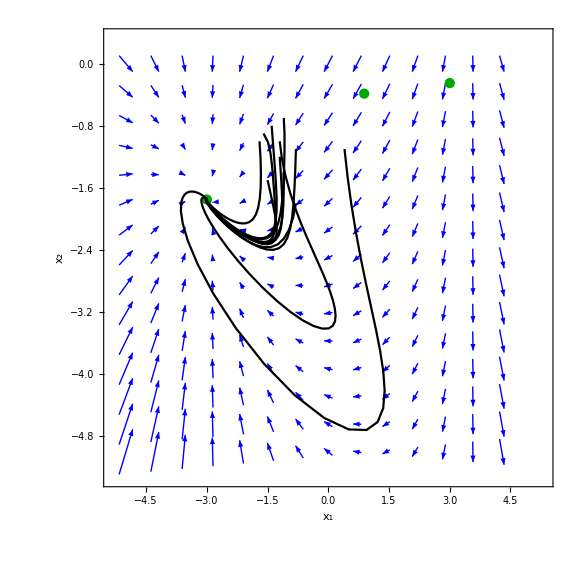

```mathematica
v2=VectorPlot[{f1[x1,x2,3.5,2.25],f2[x1,x2,3.5,2.25]},{x1,-5,5},{x2,-5,0},ImageSize->Large,Frame->True,FrameLabel->{"x_1","x_2"},VectorScale->Small,VectorStyle->Blue];
p2=ListPlot[{{-3.3860009363293826,3.8860009363293826},{0.8860009363293826,-0.3860009363293826},{3.,-0.25},{-3.,-1.75}},ImageSize->Large,AxesLabel->{"x_1","x_2"},PlotStyle->{Darker[Green],Thick}];
s11=ParametricPlot[Evaluate[{x1[t],x2[t]}/.ds01],{t,0,200},ImageSize->Large,AxesLabel->{"x_1","x_2"},PlotStyle->Black];
s12=ParametricPlot[Evaluate[{x1[t],x2[t]}/.ds02],{t,0,200},ImageSize->Large,AxesLabel->{"x_1","x_2"},PlotStyle->Black];
s13=ParametricPlot[Evaluate[{x1[t],x2[t]}/.ds03],{t,0,200},ImageSize->Large,AxesLabel->{"x_1","x_2"},PlotStyle->Black];
s14=ParametricPlot[Evaluate[{x1[t],x2[t]}/.ds04],{t,0,200},ImageSize->Large,AxesLabel->{"x_1","x_2"},PlotStyle->Black];
s15=ParametricPlot[Evaluate[{x1[t],x2[t]}/.ds05],{t,0,200},ImageSize->Large,AxesLabel->{"x_1","x_2"},PlotStyle->Black];
s16=ParametricPlot[Evaluate[{x1[t],x2[t]}/.ds06],{t,0,200},ImageSize->Large,AxesLabel->{"x_1","x_2"},PlotStyle->Black];
s17=ParametricPlot[Evaluate[{x1[t],x2[t]}/.ds07],{t,0,200},ImageSize->Large,AxesLabel->{"x_1","x_2"},PlotStyle->Black];
s18=ParametricPlot[Evaluate[{x1[t],x2[t]}/.ds08],{t,0,200},ImageSize->Large,AxesLabel->{"x_1","x_2"},PlotStyle->Black];
s19=ParametricPlot[Evaluate[{x1[t],x2[t]}/.ds09],{t,0,200},ImageSize->Large,AxesLabel->{"x_1","x_2"},PlotStyle->Black];
s110=ParametricPlot[Evaluate[{x1[t],x2[t]}/.ds10],{t,0,200},ImageSize->Large,AxesLabel->{"x_1","x_2"},PlotStyle->Black];
s111=ParametricPlot[Evaluate[{x1[t],x2[t]}/.ds11],{t,0,200},ImageSize->Large,AxesLabel->{"x_1","x_2"},PlotStyle->Black];
s112=ParametricPlot[Evaluate[{x1[t],x2[t]}/.ds12],{t,0,200},ImageSize->Large,AxesLabel->{"x_1","x_2"},PlotStyle->Black];

Show[v2,p2,s11,s12,s13,s14,s15,s16,s17,s18,s19,s110,s111,s112]
```